# Projekt za Računalniška orodja v matematiki

## 20.8.2023

## Podatki, ki jih bomo uporabili

```mathematica
ResourceSearch["wildfires"]
```

Posodobimo podatke:

```mathematica
ResourceUpdate["Total Wildland Fires and Acres (1926-2019)"]
```

ResourceObject::newest: The most recent version of resource ef2219f4-4dfc-4682-9afb-b3e01ac0b78e is already downloaded.

ResourceObject[…]

Shranimo podatke:

```mathematica
podatki = ResourceData["Total Wildland Fires and Acres (1926-2019)"]
```

Uvozimo podatke iz datoteke csv.

```mathematica
PovprecneTemperature = Import["https://raw.githubusercontent.com/Juree14/Projekt-ROM/main/Povprecna%20letna%20tem.%20v%20ZDA.csv", "CSV"]
```

{{1926,12.16},{1927,11.38},{1928,10.38},{1929,9.611},{1930,9.666},{1931,9.944},{1932,9},{1933,10.27},{1934,12.94},{1935,11.05},{1936,11.22},{1937,10.77},{1938,11.11},{1939,10.94},{1940,12.11},{1941,10.83},{1942,9.833},{1943,11.22},{1944,9.666},{1945,10.27},{1946,11.11},{1947,10.88},{1948,10.33},{1949,10.05},{1950,10.88},{1951,10.22},{1952,10.61},{1953,11.77},{1954,11.55},{1955,9.777},{1956,10.83},{1957,10.94},{1958,12},{1959,10.94},{1960,11.05},{1961,11.27},{1962,10.33},{1963,10.5},{1964,9.055},{1965,10.27},{1966,11.33},{1967,11.05},{1968,10.16},{1969,11.11},{1970,10.88},{1971,10.27},{1972,11.27},{1973,10.77},{1974,11.61},{1975,10.44},{1976,10.88},{1977,11.77},{1978,11.83},{1979,11.5},{1980,11.55},{1981,12.38},{1982,10.55},{1983,11.94},{1984,10.55},{1985,11.05},{1986,11.5},{1987,11.88},{1988,11.83},{1989,11.22},{1990,11.88},{1991,10.99},{1992,12},{1993,10.16},{1994,12.61},{1995,12.16},{1996,12.38},{1997,11.88},{1998,11.61},{1999,11.83},{2000,12.05},{2001,12.11},{2002,11.11},{2003,12.77},{2004,11.16},{2005,11.88},{2006,12.11},{2007,12.11},{2008,11.05},{2009,11.16},{2010,11.5},{2011,10.99},{2012,13.66},{2013,11.83},{2014,13.11},{2015,13.49},{2016,13.44},{2017,13.38},{2018,13.44},{2019,11.66}}

## Analiza Podatkov

Spodnji graf predstavlja količino akrov gozdov požganih od leta 1926 do leta 2019.

```mathematica
years = podatki[[All, "Year"]];
acres = podatki[[All, "Acres"]];
fires = podatki[[All, "Fires"]];
```

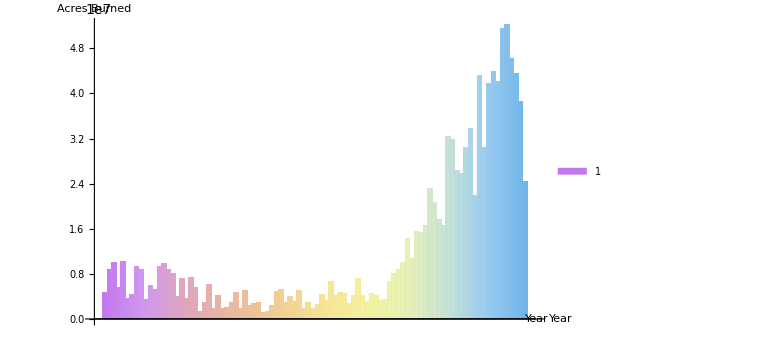

```mathematica
BarChart[acres,
ChartLabels -> years, 
 ChartStyle -> "Pastel", 
 ChartLegends -> Placed[{"Acres Burned"}, {0.15, 0.75}],
 ImageSize -> Large, 
 AxesLabel -> {"Year", "Acres Burned"}]
```

Spodnji graf prikazuje število požarov od leta 1926 do leta 2019.

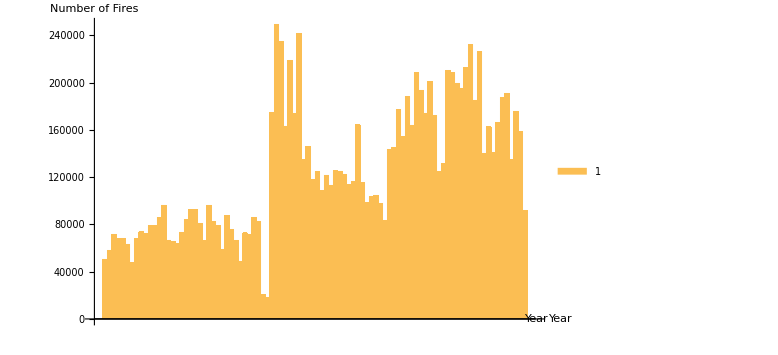

```mathematica
BarChart[fires, 
  ChartLabels ->years, 
  ChartStyle -> "Gradients", 
  ChartLegends -> Placed[{"Number of Fires"}, {0.15, 0.75}],
  ImageSize -> Large, 
  AxesLabel -> {"Year", "Number of Fires"}]
```

Spodnji graf prikazuje povprečne letne temperature in premico, ki povezuje povprečja.

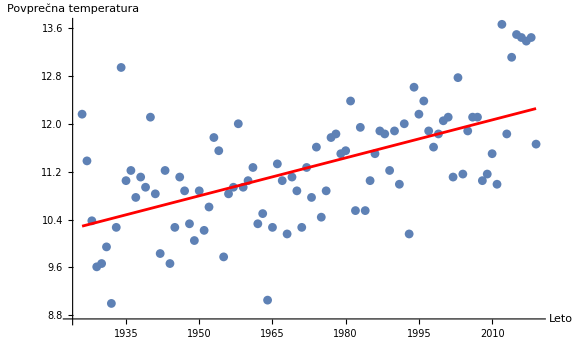

```mathematica
koordinate = Transpose[{data[[All, 1]], data[[All, 2]]}];

najboljsaPremica = LinearModelFit[koordinate, x, x];

Show[
 ListPlot[koordinate, LabelingFunction -> Tooltip, ImageSize -> Large, DataRange -> {2001, 2014}, AxesLabel -> {"Leto", "Povprečna temperatura"}],
 Plot[najboljsaPremica[x], {x, 1926, 2019}, PlotStyle -> Red]]
```

Kot lahko razberemo iz grafa opazimo da je povprečna letna temperatura narasla in je lahko razlog za povečanje gozdnih požarov.